```mathematica
dNdξ[ξ_,η_]:={1/4 (-1+η),(1-η)/4,(1+η)/4,1/4 (-1-η)};
dNdη[ξ_,η_]:={1/4 (-1+ξ),1/4 (-1-ξ),(1+ξ)/4,(1-ξ)/4};

computeBandJ[defPos_,ξ_,η_]:=Module[{X,Y,j11,j12,j21,j22,detJ,Jinv11,Jinv12,Jinv21,Jinv22,Jmat,Nmat,Dmat,B},

X=defPosᵀ⟦1⟧;
Y=defPosᵀ⟦2⟧;

j11 =X.dNdξ[ξ,η];
j12 =Y.dNdξ[ξ,η];
j21 =X.dNdη[ξ,η];
j22 =Y.dNdη[ξ,η];

detJ=j11 j22 - j12 j21;


Jinv11=j22 / detJ;
Jinv12 =-j12 / detJ;
Jinv21=-j21 / detJ;
Jinv22 = j11 / detJ;

Dmat={{1.0,0,0,0},{0,0,0,1.0},{0,1.0,1.0,0}};

Jmat ={{Jinv11,Jinv12,0,0},{Jinv21,Jinv22,0,0},{0,0,Jinv11,Jinv12},{0,0,Jinv21,Jinv22}};

Nmat={Riffle[dNdξ[ξ,η],{0,0,0,0}],Riffle[dNdη[ξ,η],{0,0,0,0}],Riffle[{0,0,0,0},dNdξ[ξ,η]],Riffle[{0,0,0,0},dNdη[ξ,η]]};


B=Dmat.Jmat.Nmat;


Return[{B,detJ}]
];


computeYieldFunction[Y_,H_,β_,pressure_,ϵp_]:=Module[{hard},

hard=Y+H ϵp;

Return[Sqrt[2./3.](β pressure + hard)];
]


computeNormalDirection[Sij_,S_,β_]:=Module[{k,temp,mag},

temp=3/2 Sqrt[2/3] Sij/S+1/3 β IdentityMatrix[3];

mag=Sqrt[Sum[temp⟦i,j⟧ temp⟦i,j⟧,{i,1,3},{j,1,3}]];

Return[temp/mag]
]


computeStress[σn_,Δd_,B_,Ey_,ν_,Y_,H_,β_,ϵp_,stepNPlasticFlag_]:=Module[{Δϵ,Cmat,σtr,Str,S,K,Pnp1,σnp1,temp,Δϵkk,Δϵd,Sn,SnMag,Sij,μ,pressure,Δλ,Qij,ΔS,x,Snp1,Δϵp,σzz,σzzN,stepNP1PlasticFlag,ΔϵdQij},

(*Compute strain increment*)
Δϵ=B.Flatten[Δd];

(*Compute an elastic trial stress (plane strain)*)
Cmat=Ey/((1.+ν)(1.-2.ν)){{(1-ν),ν ,0},{ν,(1-ν),0},{0,0,(1.-2.ν)}};

σtr=σn+Cmat.Δϵ;

(*from Hooke's law and the plane strain condition, σzz*)
σzzE=ν(σtr⟦1⟧+σtr⟦2⟧);

(*Compute deviatoric trial stress and switch to tensor notation*)
Str={{σtr⟦1⟧,σtr⟦3⟧,0},{σtr⟦3⟧,σtr⟦2⟧,0},{0,0,σzzE}}-1/3(σtr⟦1⟧+σtr⟦2⟧+σzzE)IdentityMatrix[3];

(*Compute deviatoric trial stress magnitude*)
S=Sqrt[Sum[Str⟦i,j⟧ Str⟦i,j⟧,{i,1,3},{j,1,3}]];


(*σzz under plastic loading that is consistent with normality rule*)
σzzP=1/2 ((σtr⟦1⟧+σtr⟦2⟧)+(√3 β √((9-β^2) (4 σtr⟦3⟧^2+(σtr⟦1⟧-σtr⟦2⟧)^2)))/(β^2-9));

(*this is the effective pressure at the yield surface, the σzz term comes from enforcing the plastic z-direction strains are 0 under the normality condition*)
pressure=-1/3(σtr⟦1⟧+σtr⟦2⟧+σzzP);

(*Check for yielding*)
If[Re[S]≤  Re[computeYieldFunction[Y,H,β,pressure,ϵp]],
(*not yielding, trial stress is new stress*)
σnp1=σtr;
Δϵp=0;
stepNP1PlasticFlag=0,
(*else, possibly yielding*)

(*compute dilatation increment*)
Δϵkk=1/3(Δϵ⟦1⟧+Δϵ⟦2⟧);
(*compute deviatoric strain increment*)
Δϵd={{Δϵ⟦1⟧,Δϵ⟦3⟧,0},{Δϵ⟦3⟧,Δϵ⟦2⟧,0},{0,0,0}}-Δϵkk IdentityMatrix[3];

(*compute old deviatoric stress (at step N)*)
Sn={{σn⟦1⟧,σn⟦3⟧,0},{σn⟦3⟧,σn⟦2⟧,0},{0,0,σzzE}}-1/3(σn⟦1⟧+σn⟦2⟧+σzzE)IdentityMatrix[3];
(*Deviatoric stress magnitude at step N*)
SnMag=Sqrt[Sum[Sn⟦i,j⟧ Sn⟦i,j⟧,{i,1,3},{j,1,3}]];

μ=Ey/(2(1+ν));

(*recompute the "trial" deviatoric stress with the plastic σzz term*)
Str={{σtr⟦1⟧,σtr⟦3⟧,0},{σtr⟦3⟧,σtr⟦2⟧,0},{0,0,σzzP}}-1/3(σtr⟦1⟧+σtr⟦2⟧+σzzP)IdentityMatrix[3];
(*Compute deviatoric trial stress magnitude*)
S=Sqrt[Sum[Str⟦i,j⟧ Str⟦i,j⟧,{i,1,3},{j,1,3}]];

Qij=computeNormalDirection[Str,S,β];

ΔϵdQij=Sum[Δϵd⟦i,j⟧ Qij⟦i,j⟧,{i,1,3},{j,1,3}];

(*compute for Δλ*)
Δλ=(3 (√6 SnMag-2 Y-2 pressure β-2 H ϵp+4 ΔϵdQij μ))/(2 (√6 H+6 μ));

(*Determine if yielding*)
If[Re[Δλ]≤ 0.,
(*not yielding, trial stress is new stress*)
σnp1=σtr;
Δϵp=0.;
stepNP1PlasticFlag=0,
(*yielding*)

(*update deviatoric stress*)

Snp1=computeYieldFunction[Y,H,β,pressure,ϵp+Sqrt[2/3]Δλ]*Qij;

(*update stress vector*)
σnp1={Snp1⟦1,1⟧,Snp1⟦2,2⟧,Snp1⟦1,2⟧}-pressure*{1,1,0};
Δϵp=Sqrt[2/3]Δλ;
stepNP1PlasticFlag=1
];
];

Return[{σnp1,Δϵ,Δϵp,stepNP1PlasticFlag}]
];


computeForce[defPos_,disp_,Ey_,ν_,Y_,H_,β_,ϵp1_,ϵp2_,ϵp3_,ϵp4_,σ1n_,σ2n_,σ3n_,σ4n_,stepNPlasticFlag1_,stepNPlasticFlag2_,stepNPlasticFlag3_,stepNPlasticFlag4_]:=Module[{B1,B2,σ2,B3,B4,J1,J2,J3,J4,σ1np1,σ2np1,σ3np1,σ4np1,Δϵ1,Δϵ2,Δϵ3,Δϵ4,Δϵp1,Δϵp2,Δϵp3,Δϵp4,stepNP1PlasticFlag1,stepNP1PlasticFlag2,stepNP1PlasticFlag3,stepNP1PlasticFlag4},


{B1,J1}=computeBandJ[defPos,-Sqrt[1/3.],-Sqrt[1/3.]];
{σ1np1,Δϵ1,Δϵp1,stepNP1PlasticFlag1}=computeStress[σ1n,disp,B1,Ey,ν,Y,H,β,ϵp1,stepNPlasticFlag1];

{B2,J2}=computeBandJ[defPos,-Sqrt[1/3.],Sqrt[1/3.]];
{σ2np1,Δϵ2,Δϵp2,stepNP1PlasticFlag2}=computeStress[σ2n,disp,B2,Ey,ν,Y,H,β,ϵp2,stepNPlasticFlag2];

{B3, J3}=computeBandJ[defPos,Sqrt[1/3.],-Sqrt[1/3.]];
{σ3np1,Δϵ3,Δϵp3,stepNP1PlasticFlag3}=computeStress[σ3n,disp,B3,Ey,ν,Y,H,β,ϵp3,stepNPlasticFlag3];

{B4,J4}=computeBandJ[defPos,Sqrt[1/3.],Sqrt[1/3.]];
{σ4np1,Δϵ4,Δϵp4,stepNP1PlasticFlag4}=computeStress[σ4n,disp,B4,Ey,ν,Y,H,β,ϵp4,stepNPlasticFlag4];


Return[{B1ᵀ.σ1np1 J1+B2ᵀ.σ2np1 J2+B3ᵀ.σ3np1 J3+B4ᵀ.σ4np1 J4,σ1np1,σ2np1,σ3np1,σ4np1,Δϵ1,Δϵ2,Δϵ3,Δϵ4,Δϵp1,Δϵp2,Δϵp3,Δϵp4,stepNP1PlasticFlag1,stepNP1PlasticFlag2,stepNP1PlasticFlag3,stepNP1PlasticFlag4}]

];


computeTangentStiffness[defPos_,disp_,Ey_,ν_,Y_,H_,β_,ϵp1_,ϵp2_,ϵp3_,ϵp4_,σ1_,σ2_,σ3_,σ4_,stepNPlasticFlag1_,stepNPlasticFlag2_,stepNPlasticFlag3_,stepNPlasticFlag4_]:=Module[{h,k},

h=1×10^-50;

k=Map[computeForce[defPos,Partition[#,2],Ey,ν,Y,H,β,ϵp1,ϵp2,ϵp3,ϵp4,σ1,σ2,σ3,σ4,stepNPlasticFlag1,stepNPlasticFlag2,stepNPlasticFlag3,stepNPlasticFlag4]⟦1⟧&,IdentityMatrix[2Length[nodes]]*I h];

Return[-Im[kᵀ]/h]

];
```

```mathematica
(*Setup problem*)
nodes={{0.0,0.0},{1.0,0.0},{1.0,1.0},{0.0,1.0}};
disp=ConstantArray[{0.0,0.0},Length[nodes]];
defPos = nodes;
Ey=200;
ν=0.29;
Y=15;
H=0;
β=0.0;
ϵpn=0.0;
σ1n={0.,0.,0.};
σ2n={0.,0.,0.};
σ3n={0.,0.,0.};
σ4n={0.,0.,0.};
ϵ1={0.,0.,0.};
ϵ2={0.,0.,0.};
ϵ3={0.,0.,0.};
ϵ4={0.,0.,0.};
ϵp1=0.;
ϵp2=0.;
ϵp3=0.;
ϵp4=0.;
stepNPlasticFlag1=0;
stepNPlasticFlag2=0;
stepNPlasticFlag3=0;
stepNPlasticFlag4=0;

stressStrain = {{{0.,0.,0.},{0.,0.,0.}}};

(*Begin load stepping iteration*)
Do[

PrintTemporary["Load Step = ",i];

(*Apply the initial kinematic BC's*)
disp=ConstantArray[{0.0,0.0},Length[nodes]];
disp⟦2⟧+={-0.005,0.0};
disp⟦3⟧+={-0.005,0.0};

(*Begin Newton iteration*)
Do[

(*Calculate the total force*)
{f,σ1np1,σ2np1,σ3np1,σ4np1,Δϵ1,Δϵ2,Δϵ3,Δϵ4,Δϵp1,Δϵp2,Δϵp3,Δϵp4,stepNP1PlasticFlag1,stepNP1PlasticFlag2,stepNP1PlasticFlag3,stepNP1PlasticFlag4}=computeForce[defPos,disp,Ey,ν,Y,H,β,ϵp1,ϵp2,ϵp3,ϵp4,σ1n,σ2n,σ3n,σ4n,stepNPlasticFlag1,stepNPlasticFlag2,stepNPlasticFlag3,stepNPlasticFlag4];

(*Zero residual on boundary condition nodes, they are are supposed to have reaction forces*)
f⟦{1,2,3,4,5,7}⟧={0.0,0.0,0.0,0.0,0.0,0.0};

(*Compute residual*)
res=Norm[f];

PrintTemporary["  Residual = ",res];

(*Break if convergence achieved*)
If[res<0.0000001,Break[]];

(*Compute tangent stiffness*)

K =Chop[computeTangentStiffness[defPos,disp,Ey,ν,Y,H,β,ϵp1,ϵp2,ϵp3,ϵp4,σ1n,σ2n,σ3n,σ4n,stepNPlasticFlag1,stepNPlasticFlag2,stepNPlasticFlag3,stepNPlasticFlag4]];


(*Apply essential BC's to tangent stiffness*)
K⟦1⟧=Normal@SparseArray[1-> 1,2*Length[nodes]];
K⟦2⟧=Normal@SparseArray[2-> 1,2*Length[nodes]];
K⟦3⟧=Normal@SparseArray[3-> 1,2*Length[nodes]];
K⟦4⟧=Normal@SparseArray[4-> 1,2*Length[nodes]];
K⟦5⟧=Normal@SparseArray[5-> 1,2*Length[nodes]];
K⟦7⟧=Normal@SparseArray[7-> 1,2*Length[nodes]];

(*Solve the linear problem for a displacment increment*)
disp+=Partition[LinearSolve[K,f],2];

,{j,0,50}
];

(*Update the deformed position and stresses with the converged results*)
defPos+=disp;
σ1n=σ1np1;
σ2n=σ2np1;
σ3n=σ3np1;
σ4n=σ4np1;
ϵ1+=Δϵ1;
ϵ2 +=Δϵ2;
ϵ3 +=Δϵ3;
ϵ4 +=Δϵ4;
ϵp1+=Δϵp1;
ϵp2 +=Δϵp2;
ϵp3 +=Δϵp3;
ϵp4 +=Δϵp4;
stepNPlasticFlag1=stepNP1PlasticFlag1;
stepNPlasticFlag2=stepNP1PlasticFlag2;
stepNPlasticFlag3=stepNP1PlasticFlag3;
stepNPlasticFlag4=stepNP1PlasticFlag4;

AppendTo[stressStrain,{σ3n,ϵ3}]

,{i,50}
]
```

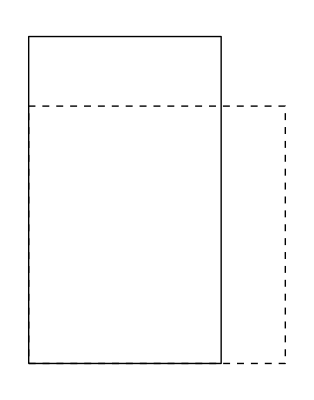

```mathematica
Graphics[{{Dashed,Line[{nodes⟦1⟧,nodes⟦2⟧,nodes⟦3⟧,nodes⟦4⟧,nodes⟦1⟧}]},{Line[{defPos⟦1⟧,defPos⟦2⟧,defPos⟦3⟧,defPos⟦4⟧,defPos⟦1⟧}]}}]
```

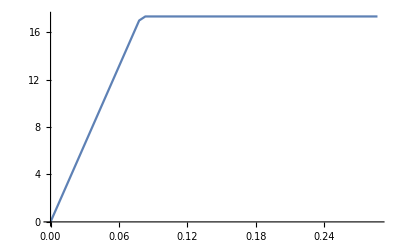

```mathematica
stress=stressStrain[[All,1]][[All,1]];
strain=stressStrain[[All,2]][[All,1]];

ListLinePlot[{-strain,-stress}ᵀ]
```